```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", "C:/Users/pdbru/Desktop/tesis/mathematica/NoisyQuantumTeleportationBenchmarking.wl"]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
contours = Association[{}];
```

```mathematica
newStyle[x_]:=x/. l_Line:>Sequence[Opacity[.4],Thick,Dashed,Red,l];
```

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist}, 
th = GetDistanceThreshold[d];
(*Export["./contours/contour-"<> GetChannelOutputFantasyName[chA] <> "-" <> GetChannelOutputFantasyName[chB] <> "-" <> GetDistanceOutputFantasyName[d] <> ".png", plot*)
plot = ContourPlot[AvgDist[pA, pB],{pA,0,1},{pB,0,1},
AxesLabel->{Subscript[p, a], Subscript[p, b]}, Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[d, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
PlotLabel->"Alice: "<>GetChannelLabel[chA]<>"\nBob: "<>GetChannelLabel[chB]<>"\nDistancia: "<>GetDistanceLabel[d]
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];

AssociateTo[contours,{chA, chB, d} -> plot];
]]
```

```mathematica
plots=Partition[(Show[#, ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> {FontFamily ->  "LM Roman 12"}])& /@ Values[contours], 4];
```

```mathematica
labelColumnas  = Prepend[MaTeX["\\text{"<>#<>"}"]&/@GetDistanceLabel/@Distances, ""];
labelFilas = MaTeX["\\text{"<>#<>"}"]&/@Flatten[Table["A: "<>GetChannelOutputFantasyName[chA]<>"\nB: "<>GetChannelOutputFantasyName[chB], {chA, Channels}, {chB, Channels}]];
```

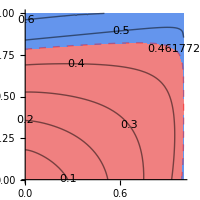
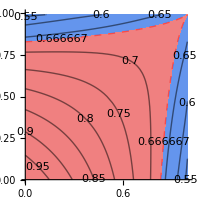
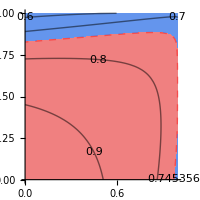
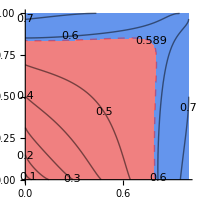
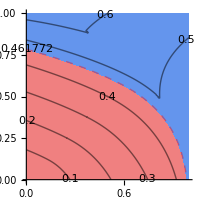
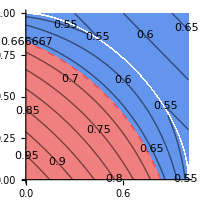
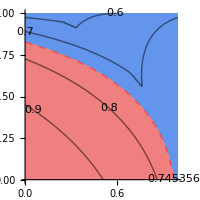
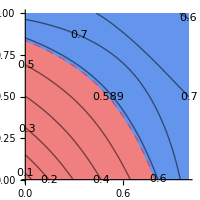
| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Do[Print[Grid[{labelColumnas}~Join~partition]], {partition, Partition[Transpose[{Rotate[#,Pi/2]&/@labelFilas}~Join~Transpose[plots]], 4]}]
```

```mathematica
plots[[1]][[4]]
```

-Graphics-